# Components of variability

This notebook explores how changing components of temperature vs supply can change our landscape-level variation in ϕ

## Parameters & Helpers

First, declare all the various helpers, including what we’re going to call each of the different variables, and where things are stored. Then we’ll write a main “simulation” function as well as a series of helper functions

```mathematica
(* ----------------------------------------------------------------------- *)
(* 00  Directory helpers *)
(* ----------------------------------------------------------------------- *)
Off[General::munfl] (* suppress underflow warnings that clutter the log *)

(* main figure directory (relative to this notebook) *)
figDir = FileNameJoin[{
  NotebookDirectory[], "..", "..", "figs", "si", "s-vs-t-variability"
}];
If[! DirectoryQ[figDir],
  CreateDirectory[figDir, CreateIntermediateDirectories -> True]
];

(* data directory for binary objects *)
dataDir = FileNameJoin[{
  NotebookDirectory[], "..", "..", "outputs", "intermediate-obs",
  "s-vs-t-variability"
}];
If[! DirectoryQ[dataDir],
  CreateDirectory[dataDir, CreateIntermediateDirectories -> True]
];
  
(* ----------------------------------------------------------------------- *)
(* 01  Environmental response functions *)
(* ----------------------------------------------------------------------- *)

ClearAll[ImaxFunc, RespirationFunc, SuitabilityFunc];

(* ::Usage:: *)
(* ImaxFunc[T, optT, respBreadth] returns the maximum intake rate scaled by a *)
(* Gaussian thermal performance curve centred on optT with breadth           *)
(* respBreadth. *)

(* TODO: adjust TI / gamma for species‑specific thermal curve *)
ImaxFunc[T_, optT_, respBreadth_] :=
  Exp[-((T - optT)^2)/respBreadth];

(* ::Usage:: *)
(* RespirationFunc[T, {ma, mb, mc}] returns temperature‑dependent metabolic   *)
(* maintenance cost m(T) = ma * exp(mb * T) + mc. *)

(* TODO: refine metabolic parameters ma, mb, mc *)
RespirationFunc[T_, {ma_, mb_, mc_}] :=
  ma*Exp[mb*T] + mc;

(* ::Documentation:: *)
(* SuitabilityFunc[T, R, params] *)
(*   ‣ T: temperature of patch i (°C) *)
(*   ‣ R: resource availability of patch i *)
(*   ‣ params: <| "optT" -> ..., "respBreadth" -> ..., *)
(*               "Rhalf" -> ..., "mParams" -> {...} |> *)
(* Returns the biological suitability of a patch given thermal intake and    *)
(* metabolic costs. Negative values (i.e. cost > gain) are truncated to 0. *)

SuitabilityFunc[T_, R_, params_Association] :=
 Module[{imax, m},
   imax = ImaxFunc[T, params["optT"], params["respBreadth"]];
   m = RespirationFunc[T, params["mParams"]];
   Max[0, (imax*R)/(R + params["Rhalf"]) - m]
 ];

 
(* ----------------------------------------------------------------------- *)
(* 01a  Packed suitability calculation (compiled C kernel) *)
(* ----------------------------------------------------------------------- *)

ClearAll[SuitabilityArrayC];

(* ::Documentation:: *)
(* SuitabilityArrayC[Tmat, Rmat, optT, respB, Rh, ma, mb, mc] *)
(*   Fast element‑wise evaluation of SuitabilityFunc on matrices of          *)
(*   temperatures (Tmat) and resources (Rmat). Implemented with              *)
(*   Compile[..., CompilationTarget -> "C"]. *)

SuitabilityArrayC = Compile[
  {{Tmat, _Real, 2}, {Rmat, _Real, 2}, {optT, _Real}, {respB, _Real},
   {Rh, _Real}, {ma, _Real}, {mb, _Real}, {mc, _Real}},
  Module[{imax, m, expr},
    imax = Exp[-((Tmat - optT)^2)/respB];
    m = ma*Exp[mb*Tmat] + mc; (* exponential metabolic term *)
    expr = (imax*Rmat)/(Rmat + Rh) - m;
    expr*UnitStep[expr] (* element‑wise max(0, expr) *)
  ],
  RuntimeOptions   -> "Speed",
  CompilationTarget-> "C"
];
 
  
(* ----------------------------------------------------------------------- *)
(* 02  Compiled φ kernels *)
(* ----------------------------------------------------------------------- *)


(* ----------------------------------------------------------------------- *)
(* 02  Compiled φ kernels *)
(* ----------------------------------------------------------------------- *)

ClearAll[CompiledPhiConst, CompiledPhiVec, ComputePhiBatch];

(* ::Documentation:: *)
(* CompiledPhiConst[w, eps, S] *)
(*   φ = Σ_i [1 - (1 - w_i * eps)^S] when eps is a scalar. probability of a
     disease spreading on the landscape from cell i, assuming I = 1, 
     ϕi(k, I = 1) is 1 − (1 − w(T )ε(T ))^S, so as long as I = 1, we set 
     the number of susceptibles, S, then calculate the temperature-dependent 
     probability of spread (eps), then get the patch weight, and multiply. The 
     challenge here is speed, so there's two versions - one for if the env. resp.
     is just a scalar or if it's a function of T.*)
(* CompiledPhiVec[w, epsV, S] *)
(*   Same as above but epsV is a vector of per‑patch probabilities. *)

CompiledPhiConst = Compile[
  {{w, _Real, 1}, {eps, _Real}, {S, _Integer}},
  Total[w * ( 1 - (1 - w*eps)^S)],
  RuntimeOptions   -> "Speed",
  CompilationTarget-> "C"
];

CompiledPhiVec = Compile[
  {{w, _Real, 1}, {epsV, _Real, 1}, {S, _Integer}},
  Total[w * (1 - (1 - w*epsV)^S)],
  RuntimeOptions   -> "Speed",
  CompilationTarget-> "C"
];

(* ----------------------------------------------------------------------- *)
(* 03  ComputePhiBatch — mean & sd over many landscapes without storing *)
(* ----------------------------------------------------------------------- *)

(* ::Documentation:: *)
(* ComputePhiBatch[nPatches, meanT, varT, meanR, varR, suitParams, totalS,   *)
(*                 epsF, nReps, batchSize] *)
(* it's easier to compute a number of independent landscapes that a single 
  kernel can generate and evaluate at one time, before it updates the running
  mean / variance. Soo, trying to do that here by batch-computing the 
  landscapes, which should simplify the whole situation. 
          *   nPatches, meanT, varT, meanR, varR, suitParams: landscape cont.
          *   totalS, epsF: epidemiological cont.
          *   nReps, batchSize: simulation cont.
  Returns {Mean[φ], SD[φ]} based on nReps stochastic landscapes, using 
  batches of size 'batchSize' to keep RAM flat and to amortise 
  compiled‑kernel overhead. Hopefully hehe!
*)
ComputePhiBatch[nPatches_, meanT_, varT_, meanR_, varR_, suitParams_,
                totalS_, epsF_, nReps_, batchSize_] :=
 Module[{count = 0, mean = 0., M2 = 0., repsLeft = nReps,
         b, Tmat, Rmat, raw, w, epsMat, phiBatch,
         optT, respB, Rh, ma, mb, mc},
  
  (* pull scalars once, outside the loop *)
  optT = suitParams["optT"]; 
  respB = suitParams["respBreadth"];
  Rh = suitParams["Rhalf"]; 
  {ma, mb, mc} = suitParams["mParams"];
  
  While[repsLeft > 0,
   b = Min[batchSize, repsLeft];
   Tmat = Developer`ToPackedArray@
           RandomVariate[NormalDistribution[meanT, varT], {b, nPatches}];
   Rmat = Developer`ToPackedArray@
           RandomVariate[NormalDistribution[meanR, varR], {b, nPatches}];
   
   raw  = SuitabilityArrayC[Tmat, Rmat, optT, respB, Rh, ma, mb, mc];
   w = raw/Total[raw, {2}]; (* b × nPatches, rows sum 1 *)

   (* --------------------------------------------------------------- *)
   phiBatch =
     If[NumericQ[epsF],
       CompiledPhiConst[#, epsF, totalS] & /@ w, (* map row‑wise *)
       (
         epsMat = epsF[Tmat];
         MapThread[CompiledPhiVec[#1, #2, totalS] &, {w, epsMat}]
       )
     ];
   (* --------------------------------------------------------------- *)

   (* streaming mean/variance update (Welford) *)
   Do[
     count++;
     With[{delta = φ - mean},
       mean += delta/count;
       M2   += delta (φ - mean)];
     ,
     {φ, phiBatch}
   ];
   
   repsLeft -= b;
  ];
  
  {mean, If[count > 1, Sqrt[M2/(count - 1)], 0.]}
]


(* ----------------------------------------------------------------------- *)
(* 04  SimulateTransmissionDataset — flat table or tensor on request *)
(* ----------------------------------------------------------------------- *)

Options[SimulateTransmissionDataset] = {
  "Format"   -> "Dataset",
  "BatchSize"-> Automatic
};

(* ::Documentation:: *)
(* SimulateTransmissionDataset[nReps, nPatches, totalS, varRList, varTList,   *)
(*                            meanRList, meanTList, suitParams, epsF, opts]  *)
(*   Computes φ‑statistics across all parameter combinations.                *)
(*   • "Format" -> "Dataset" (default) returns a readable Dataset.            *)
(*   • "Format" -> "Tensor" returns the original nested tensor structure.    *)
(* this is a simulation with all the parameters explicit so we have a batched 
  and compiled driver that can switch back and forth between an output that
  is human-readable, and then a tensor output that is probably a bit more eff. 
*)
SimulateTransmissionDataset[nReps_, nPatches_, totalS_, varRList_, varTList_,
                            meanRList_, meanTList_, suitParams_, epsF_,
                            opts : OptionsPattern[]] :=
 Module[{format    = OptionValue["Format"],
         batchSize = Replace[OptionValue["BatchSize"],
                             Automatic :> Min[128, nReps]],
         combos, results},
  
  If[! MemberQ[{"Dataset", "Tensor"}, format],
    Message[SimulateTransmissionDataset::badfmt, format];
    Return[$Failed]];
  
  (* all parameter combinations *)
  combos = Tuples[{varTList, varRList, meanTList, meanRList}];
  
  (* parallel over combos — each worker chews through all its nReps *)
  results = ParallelMap[
    Function[{pars},
      With[{varT  = pars[[1]], varR  = pars[[2]],
            meanT = pars[[3]], meanR = pars[[4]],
            stats = ComputePhiBatch[nPatches, meanT, varT,
                                    meanR,  varR, suitParams,
                                    totalS, epsF, nReps, batchSize]},
        AssociationThread[
          {"varT", "varR", "meanT", "meanR", "phiMean", "phiSD"},
          Join[pars, stats]
        ]
      ]
    ],
    combos
  ];
  
  Which[
    format === "Dataset",
      Dataset[results],
    
    format === "Tensor",
      Print["Not currently supported"]
  ]
];

(* ----------------------------------------------------------------------- *)
(* 05  PlotWeightHistograms – visualise w‑distributions                      *)
(* ----------------------------------------------------------------------- *)

ClearAll[PlotWeightHistograms];
Options[PlotWeightHistograms] = {"Bins" -> 40, "ChartStyle" -> Automatic,
  "ImageSize" -> 400};
(* ::Usage:: *)
(* PlotWeightHistograms[varTList, varRList, meanTList, meanRList,            *)
(*                      nPatches, suitParams, OptionsPattern[]] returns a    *)
(* GraphicsGrid of histograms showing the distribution of patch weights w_i  *)
(* for every combination of variance/mean parameters provided.               *)
(*                                                                            *)
(* Options:                                                                   *)
(*   "Bins"        -> 40        number of histogram bins                      *)
(*   "ChartStyle"  -> Automatic  passed to Histogram                          *)

PlotWeightHistograms[varTList_, varRList_, meanTList_, meanRList_,
  nPatches_, suitParams_, OptionsPattern[]] :=
 Module[{bins = OptionValue["Bins"], style = OptionValue["ChartStyle"],
   imgSize = OptionValue["ImageSize"], combos, makeW, wTable, xRange, labels,
   hists},

  (* helper to build one w‑vector *)
  makeW[varT_, varR_, meanT_, meanR_] := Module[{Tvec, Rvec, raw},
    Tvec = RandomVariate[NormalDistribution[meanT, varT], nPatches];
    Rvec = RandomVariate[NormalDistribution[meanR, varR], nPatches];
    raw = First@SuitabilityArrayC[{Tvec}, {Rvec}, suitParams["optT"],
      suitParams["respBreadth"], suitParams["Rhalf"],
      Sequence @@ suitParams["mParams"]];
    raw/Total[raw]
  ];

  combos = Tuples[{varTList, varRList, meanTList, meanRList}];
  wTable = makeW @@@ combos;                     (* list of weight vectors *)

  (* common x‑axis range over ALL combos *)
  xRange = {0, Max[Flatten[wTable]]};

  labels = Map[
    Function[{pars}, Row[{"varT=", pars[[1]], "  varR=", pars[[2]],
      "  meanT=", pars[[3]], "  meanR=", pars[[4]]}]], combos];

  hists = MapThread[
    Function[{wvec, lab},
      Histogram[wvec, bins, Frame -> True, PlotLabel -> lab,
        ChartStyle -> style, ImageSize -> imgSize, PlotRange -> {xRange, All},
        FrameTicks -> {{Automatic, None}, {Automatic, Automatic}}]
    ], {wTable, labels}];

  Column[hists, Spacings -> 1]
 ]
```

## Looking at variation in R

Start by holding everything constant and looking at how changing the variation in R might change what we see here

OptionValue::nodef: Unknown option ImageSize for PlotWeightHistograms.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

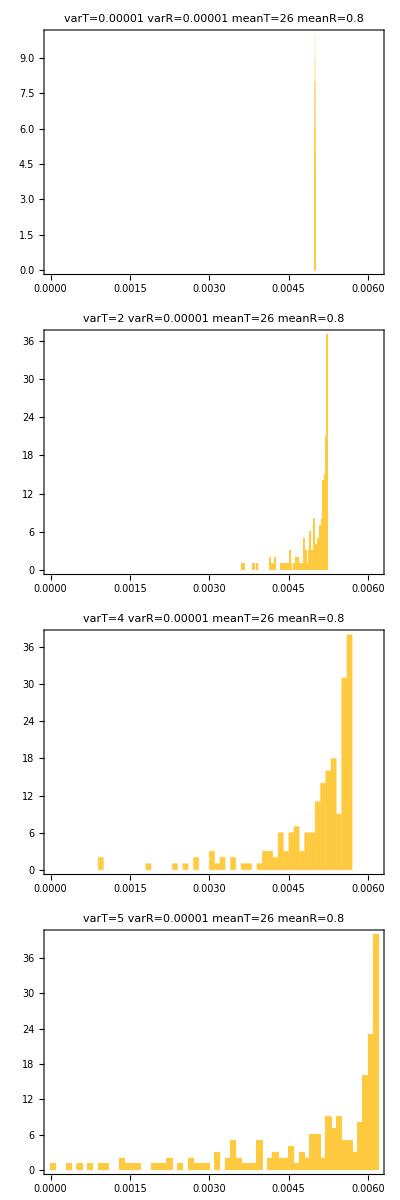

```mathematica
Options[SimulateTransmissionDataset] =               (* <— must run *)
  {"Format" -> "Dataset", "BatchSize" -> Automatic};
Options[PlotWeightHistograms] = {"Bins" -> 40, "ChartStyle" -> Automatic};

nReps     = 1000;
nPatches  = 200;
totalS    = 100;
varRList  = {0.00001};
varTList  = {0.00001, 2, 4, 5};
meanRList = {0.8};
meanTList = {26};
suitParams = <|
  "optT"        -> 25,
  "respBreadth" -> 150,
  "Rhalf"       -> 0.5,
  "mParams"     -> {0.05, 0.03, 0.01}
|>;
epsF = 1;
PlotWeightHistograms[
  varTList, varRList, meanTList, meanRList,
  nPatches, suitParams,
  "Bins" -> 50, "ImageSize" -> 350
]
tidy = SimulateTransmissionDataset[
  nReps, nPatches, totalS,
  varRList, varTList, meanRList, meanTList,
  suitParams, epsF,
  "Format" -> "Dataset",
  "BatchSize" -> 128
]
```

## Testing area

Here, I’m just going through some peace of mind tests.

### First, test that the suitability functions actually work

{0.,0.}

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

0.

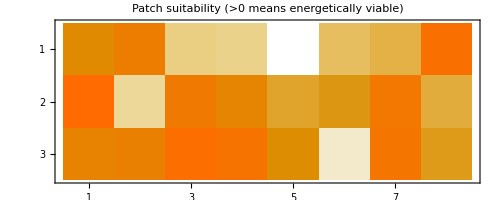

```mathematica
(* testing that the two suitability functions perform the same *)
(* --- 1. set up a toy landscape ---------------------------------------- *)
nRows   = 3;              (* number of replicated landscapes *)
nPatches = 8;             (* cells per landscape *)

Tmat = RandomVariate[NormalDistribution[20, 2], {nRows, nPatches}];
Rmat = RandomVariate[NormalDistribution[1, 0.3], {nRows, nPatches}];

params = <|
  "optT"        -> 22,
  "respBreadth" -> 5,
  "Rhalf"       -> 0.6,
  "mParams"     -> {0.3, 0.04, 0.02}
|>;

(* --- 2. reference calculation with the scalar SuitabilityFunc ---------- *)
valsScalar = MapThread[
  SuitabilityFunc[#1, #2, params] &,
  {Tmat, Rmat},
  2                          (* map at depth 2 to keep matrix shape *)
];

(* --- 3. compiled calculation ------------------------------------------ *)
valsCompiled = SuitabilityArrayC[
  Tmat, Rmat,
  params["optT"], params["respBreadth"], params["Rhalf"],
  Sequence @@ params["mParams"]
];

(* --- 4. compare -------------------------------------------------------- *)
diff = valsScalar - valsCompiled;
{minDiff, maxDiff} = Through[{Min, Max}[Flatten[diff]]]
valsCompiled
valsScalar

(* make sure I can get a set of non-zero values here *)
nRows    = 3;
nPatches = 8;

SeedRandom[1234];  (* reproducible *)

Tmat = RandomVariate[NormalDistribution[22, 1], {nRows, nPatches}];  (* nearer optT *)
Rmat = RandomVariate[NormalDistribution[5, 0.5], {nRows, nPatches}]; (* more food *)

params = <|
  "optT"        -> 22,
  "respBreadth" -> 5,
  "Rhalf"       -> 0.6,
  "mParams"     -> {0.15, 0.03, 0.01}  (* gentler metabolic curve *)
|>;

valsScalar = MapThread[
  SuitabilityFunc[#1, #2, params] &,
  {Tmat, Rmat},
  2
];

valsCompiled = SuitabilityArrayC[
  Tmat, Rmat,
  params["optT"], params["respBreadth"], params["Rhalf"],
  Sequence @@ params["mParams"]
];

(* Verify equality *)
Max[Abs[valsScalar - valsCompiled]]      (* ~1.1*10^-15 *)

(* Inspect suitability values *)
MatrixPlot[valsScalar,
  Frame -> True,
  PlotLabel -> "Patch suitability (>0 means energetically viable)"
]
```

### Let’s do a quick test run of the whole thing:

```mathematica
Options[SimulateTransmissionDataset] =               (* <— must run *)
  {"Format" -> "Dataset", "BatchSize" -> Automatic};

nReps     = 1000;
nPatches  = 200;
totalS    = 20;
varRList  = {0.1, 0.5, 0.8, 1};
varTList  = {0.1, 1, 1.5, 3, 5};
meanRList = {0.8};
meanTList = {22};
suitParams = <|
  "optT"        -> 25,
  "respBreadth" -> 150,
  "Rhalf"       -> 0.5,
  "mParams"     -> {0.05, 0.03, 0.01}
|>;
epsF      = 0.3;

tidy = SimulateTransmissionDataset[
  nReps, nPatches, totalS,
  varRList, varTList, meanRList, meanTList,
  suitParams, epsF,
  "Format" -> "Dataset",
  "BatchSize" -> 256
]
```

This is weird -- the values of the phiMean are all the same???

### Now, I want to look at a single set of parameters to see if things really make sense here

{{0.,0.00273752},1.}

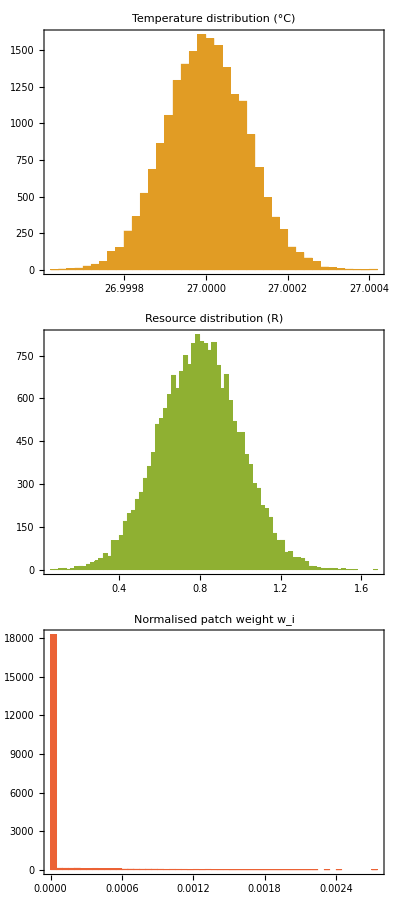

```mathematica
(* --------------------------------------------------------- *)
(* pick ONE combination you’d like to inspect                *)
varT   = 0.0001;          (* e.g. use an entry of varTList *)
varR   = 0.2;          (* e.g. use an entry of varRList *)
meanT  = 27.;          (* the only entry in your meanTList *)
meanR  = 0.8;          (* the only entry in your meanRList *)
nPatches = 20000;
nReps     = 1000;
totalS    = 20;
suitParams = <|
  "optT"        -> 21,
  "respBreadth" -> 21,
  "Rhalf"       -> 0.5,
  "mParams"     -> {0.05, 0.03, 0.01}
|>;
epsF      = 0.3;
(* --------------------------------------------------------- *)
(* 1 · simulate one landscape                                *)
Tvec = RandomVariate[
  NormalDistribution[meanT, varT],
  nPatches                           (* 20 000 cells *)
];

Rvec = RandomVariate[
  NormalDistribution[meanR, varR],
  nPatches
];

(* SuitabilityArrayC expects 2‑D matrices; wrap in {…} so we
   get a 1×nPatches row and unwrap at the end. *)
rawSuit = First @ SuitabilityArrayC[
  {Tvec}, {Rvec},
  suitParams["optT"], suitParams["respBreadth"], suitParams["Rhalf"],
  Sequence @@ suitParams["mParams"]
];

w = rawSuit/Total[rawSuit];   (* weights sum to 1 *)

(* --------------------------------------------------------- *)
(* 2 · quick sanity checks                                   *)
{MinMax[w], Total[w]} (* should be {0, something} and 1 *)

(* --------------------------------------------------------- *)
(* 3 · visualise                                              *)
Column[{
  Histogram[Tvec,
    50,
    Frame        -> True,
    PlotLabel    -> "Temperature distribution (°C)",
    ChartStyle   -> ColorData[97][2],
    ImageSize    -> Medium
  ],
  Histogram[Rvec,
    50,
    Frame        -> True,
    PlotLabel    -> "Resource distribution (R)",
    ChartStyle   -> ColorData[97][3],
    ImageSize    -> Medium
  ],
  Histogram[w,
    50,
    Frame        -> True,
    PlotLabel    -> "Normalised patch weight w_i",
    ChartStyle   -> ColorData[97][4],
    ImageSize    -> Medium
  ]
}]
```

This looks reasonable! Note though that if the R distribution goes negative (i.e. if the var is too large or whatever, then the distribution of w’s start to look really goofy.

```mathematica
Total[w*(1-(1-w*0.3)^2000000)]
```

0.999994

### Now check why it looks like all the phi’s are the same:

{0.0996412,0.116788}

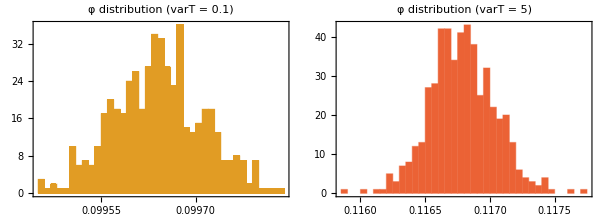

```mathematica
(* ------------------------------------------------------------------- *)
(* 0 ·  Convenience aliases & constants                                *)
(* ------------------------------------------------------------------- *)
nPatches  = 20000;
totalS    = 2000;
varRList  = {0.1, 0.5, 0.8, 1};
varTList  = {0.1, 1, 1.5, 3, 5};
meanRList = {0.8};
meanTList = {22};
suitParams = <|
  "optT"        -> 25,
  "respBreadth" -> 150,
  "Rhalf"       -> 0.5,
  "mParams"     -> {0.15, 0.03, 0.01}
|>;
epsF      = 1;

nRepsTest     = 500;           (* keep it interactive; raise if you like *)
batchSizeTest = 256;

meanT   = First[meanTList];    (* 22 *)
meanR   = First[meanRList];    (* 0.8 *)
varR    = 0.2;                 (* choose one R‑variance to hold constant *)

{optT, respB, Rh} = Lookup[suitParams, {"optT", "respBreadth", "Rhalf"}];
{ma, mb, mc}      = suitParams["mParams"];

(* ------------------------------------------------------------------- *)
(* 1 ·  Helper that returns the FULL φ list for a given varT           *)
(* ------------------------------------------------------------------- *)
ClearAll[phiSamples];
phiSamples[varT_?NumericQ] :=
 Module[{repsLeft = nRepsTest, φlist = {}, b, Tmat, Rmat, raw, w, epsMat},
  While[repsLeft > 0,
   b    = Min[batchSizeTest, repsLeft];
   Tmat = Developer`ToPackedArray@
           RandomVariate[NormalDistribution[meanT, varT], {b, nPatches}];
   Rmat = Developer`ToPackedArray@
           RandomVariate[NormalDistribution[meanR, varR], {b, nPatches}];

   raw  = SuitabilityArrayC[
     Tmat, Rmat, optT, respB, Rh, ma, mb, mc
   ];
   w    = raw/Total[raw, {2}];       (* each row sums to 1 *)

   If[NumericQ[epsF],
     φlist = Join[φlist, CompiledPhiConst[#, epsF, totalS] & /@ w],
     ( epsMat = epsF[Tmat];
       φlist = Join[
         φlist,
         MapThread[CompiledPhiVec[#1, #2, totalS] &, {w, epsMat}]
       ]
     )
   ];

   repsLeft -= b;
  ];
  φlist
]

(* ------------------------------------------------------------------- *)
(* 2 ·  Generate φ samples for two varT values                         *)
(* ------------------------------------------------------------------- *)
phi0p1 = phiSamples[0.1];
phi5   = phiSamples[5];

(* quick sanity: means should differ if variance matters *)
{Mean[phi0p1], Mean[phi5]}      (* compare *)

(* ------------------------------------------------------------------- *)
(* 3 ·  Visual comparison                                              *)
(* ------------------------------------------------------------------- *)
GraphicsRow[
  {
    Histogram[phi0p1, 40,
      Frame -> True,
      PlotLabel -> "φ distribution (varT = 0.1)",
      ChartStyle -> ColorData[97][2],
      ImageSize -> 300
    ],
    Histogram[phi5, 40,
      Frame -> True,
      PlotLabel -> "φ distribution (varT = 5)",
      ChartStyle -> ColorData[97][4],
      ImageSize -> 300
    ]
  },
  Spacings -> 2
]
```

```mathematica
SeedRandom[1234];          (* reproducible micro‑tests *)

(* shared toy parameters — tweak freely while exploring *)
params = <|"optT"->22,"respBreadth"->25,"Rhalf"->0.6,
           "mParams"->{0.05,0.05,0.02}|>;
constEps = 0.3;
epsFunc  = Function[T, 0.2 + 0.01 T];      (* any T‑dependent rule *)

nPatchesTest = 30;         (* tiny landscape for cross‑checks *)
batchSize    = 16;         (* tiny batch for speed in notebook *)
```

```mathematica
SuitabilityFunc[22., 0.8, params]
```

0.40122

{{0.424813,0.317748,0.344634,0.475924,0.351131,0.265363,0.481978,0.382188,0.474999,0.388669},3.90745}

{2,10}

{3.87012,3.42151}

{1.,1.}

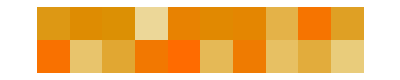

```mathematica
temp1 = RandomReal[{20,24}, 10];
sup1  = RandomReal[{0.4,1.2}, 10];

raw1  = SuitabilityArrayC[
          {temp1}, {sup1},              (* wrap in { } to get 1×10 matrix *)
          params["optT"], params["respBreadth"],
          params["Rhalf"], Sequence @@ params["mParams"]][[1]];

{raw1, Total[raw1]}  
params = <|"optT"->22,"respBreadth"->25,"Rhalf"->0.6,
          "mParams"->{0.05,0.05,0.02}|>;

b = 2; nPatches = 10;
temps = RandomReal[{20,24}, {b, nPatches}];
supp  = RandomReal[{0.4,1.2}, {b, nPatches}];

raw = SuitabilityArrayC[
        temps, supp,
        params["optT"], params["respBreadth"],
        params["Rhalf"],
        Sequence @@ params["mParams"]];

Dimensions[raw]          (* -> {2, 10} *)
Total[raw, {2}]          (* two positive numbers *)
wMat = raw/Total[raw, {2}];
Total[wMat, {2}]         (* {1., 1.} *)
MatrixPlot[wMat, Frame -> False]
```

```mathematica
S = 20;
phiConst = CompiledPhiConst[wMat[[1]], 0.3, S];
phiVec   = CompiledPhiVec[wMat[[2]], 0.2 + 0.01*temps[[2]], S];
{phiConst, phiVec}
```

{4.5296,5.67911}

```mathematica
meanSD = ComputePhiBatch[
  nPatches   = 30,
  meanT      = 22,   varT = 0.4,
  meanR      = 0.8,  varR = 0.2,
  params,                 (* Association you’ve been using *)
  totalS     = 20,
  epsF       = 0.3,        (* constant ε; try epsFunc next *)
  nReps      = 100,
  batchSize  = 25
]

(* brute‑force cross‑check *)
phiList = Table[
  With[{T = RandomReal[{21,23}, nPatches],
        R = RandomReal[{0.5,1.0}, nPatches]},
    w   = MapThread[SuitabilityFunc[#1,#2,params]&, {T,R}];
    w   = w/Total[w];
    CompiledPhiConst[
      Developer`ToPackedArray @ w,
      0.3,
      20]
  ],
  {100}
];

{meanSD, {Mean@phiList, StandardDeviation@phiList}}
```

```mathematica
Options[SimulateTransmissionDataset] =               (* <— must run *)
  {"Format" -> "Dataset", "BatchSize" -> Automatic};

nReps     = 1000;
nPatches  = 20000;
totalS    = 200;
varRList  = {0.1, 0.5, 0.8, 1};
varTList  = {0.1, 1, 1.5, 3, 5};
meanRList = {0.8};
meanTList = {22};
suitParams = <|
  "optT"        -> 25,
  "respBreadth" -> 150,
  "Rhalf"       -> 0.5,
  "mParams"     -> {0.15, 0.03, 0.01}
|>;
epsF      = 0.3;

tidy = SimulateTransmissionDataset[
  nReps, nPatches, totalS,
  varRList, varTList, meanRList, meanTList,
  suitParams, epsF,
  "Format" -> "Dataset",
  "BatchSize" -> 256
]
```